```mathematica
ctout[ct_,r_]:=ct;
rout[ct_,r_]:=r+Rs*Log[r/Rs-1];
ctin[ct_,r_]:=r+Rs*Log[1-r/Rs];
rin[ct_,r_]:=ct;
```

```mathematica
Yrightin[ct_,r_]:=(Tanh[(ctin[ct,r]+rin[ct,r])/scale]-Tanh[(ctin[ct,r]-rin[ct,r])/scale])/2-1;
Yupin[ct_,r_]:=(Tanh[(ctin[ct,r]+rin[ct,r])/scale]+Tanh[(ctin[ct,r]-rin[ct,r])/scale])/2+1;
Yrightout[ct_,r_]:=(Tanh[(ctout[ct,r]+rout[ct,r])/scale]-Tanh[(ctout[ct,r]-rout[ct,r])/scale])/2;
Yupout[ct_,r_]:=(Tanh[(ctout[ct,r]+rout[ct,r])/scale]+Tanh[(ctout[ct,r]-rout[ct,r])/scale])/2;
```

```mathematica
scale=10;
Rs=3;
```

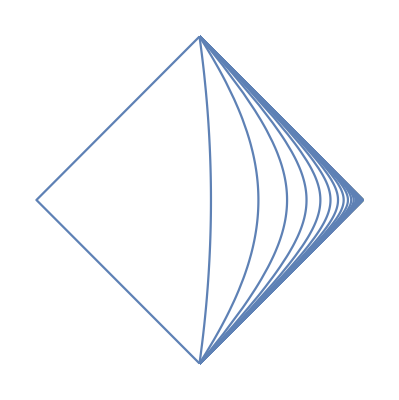

```mathematica
SpatialOut=ParametricPlot[Table[{Yrightout[tt,n+0.00000001],Yupout[tt,n+0.00000001]},{n,3,100}],{tt,-100,100},PlotRange->All,AspectRatio->Automatic,Axes->False]
```

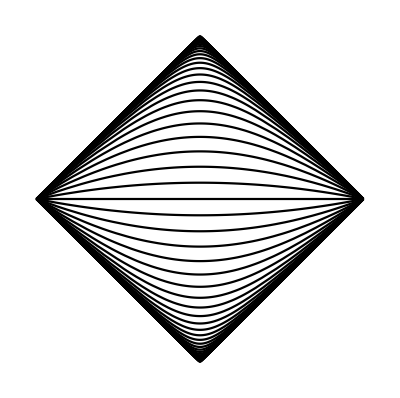

```mathematica
TemporalOut=ParametricPlot[Table[{Yrightout[nn,rr],Yupout[nn,rr]},{nn,-30,30}],{rr,3.000000001,40},Axes->False,PlotStyle->Black]
```

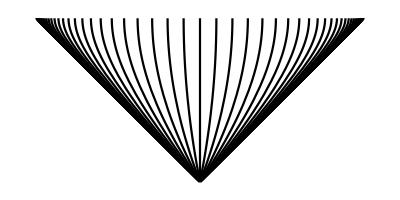

```mathematica
TemporalIn=ParametricPlot[Table[{Yrightin[nn,rr],Yupin[nn,rr]},{nn,-30,30}],{rr,0,2.999999},Axes->False,PlotStyle->Black,PlotRange->All]
```

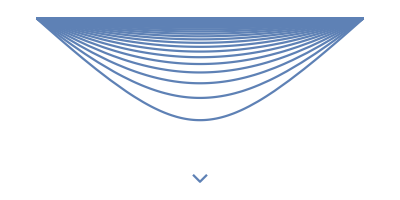

```mathematica
SpatialIn=ParametricPlot[Table[{Yrightin[tt,n/10-0.00000001],Yupin[tt,n/10-0.00000001]},{n,0,30}],{tt,-40,40},PlotRange->All,AspectRatio->Automatic,Axes->False]
```

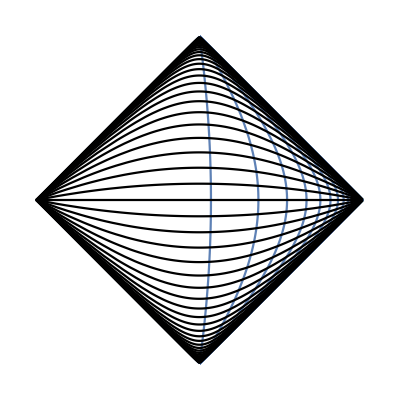

```mathematica
exterior=Show[SpatialOut,TemporalOut]
```

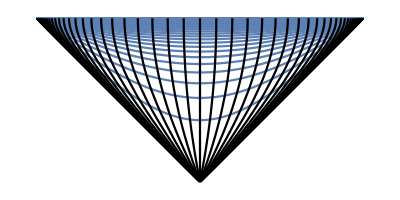

```mathematica
interior=Show[SpatialIn,TemporalIn]
```

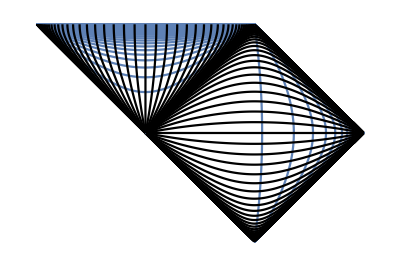

```mathematica
complete=Show[exterior,interior]
```

```mathematica
rFF[ro_,η_]:=(1+Cos[η])*ro/2;
tFF[ro_,η_]:=(ro/2+Rs)*(ro/Rs-1)^0.5*η+ro/2*(ro/Rs-1)^0.5*Sin[η]+Rs*Log[Abs[((ro/Rs-1)^0.5+Tan[η/2])/((ro/Rs-1)^0.5-Tan[η/2])]]
```

```mathematica
EtaH[ro_]:=η/.FindRoot[Rs==(1+Cos[η])*ro/2,{η,0,π}]
```

```mathematica
ManCurveout[ro_]:=ParametricPlot[{Yrightout[tFF[ro,η],rFF[ro,η]],Yupout[tFF[ro,η],rFF[ro,η]]},{η,0,EtaH[ro]}]
```

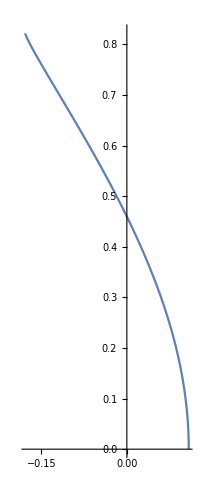

```mathematica
a=ManCurveout[4.1]
```

```mathematica
ManCurvein[ro_]:=ParametricPlot[{Yrightin[tFF[ro,η],rFF[ro,η]],Yupin[tFF[ro,η],rFF[ro,η]]},{η,EtaH[ro],π}]
```

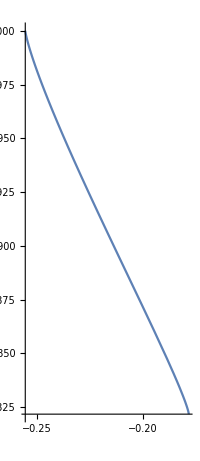

```mathematica
b=ManCurvein[4.1]
```

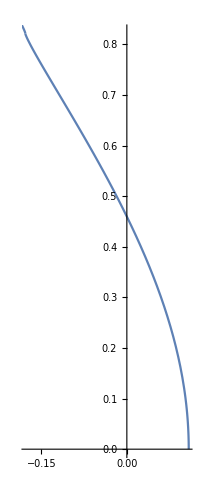

```mathematica
Show[a,b]
```

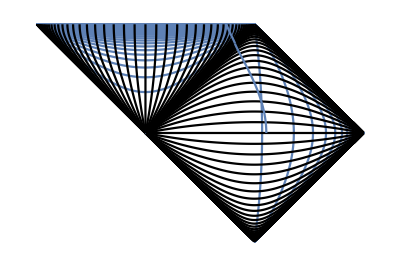

```mathematica
Show[complete,a,b]
```

```mathematica
PhotonTimeoutOut[r_,ro_]:=r-ro+Rs*Log[(r-Rs)/(ro-Rs)];
```

```mathematica
LightCurveoutOut[ro_]:=ParametricPlot[{Yrightout[PhotonTimeoutOut[r,ro],r],Yupout[PhotonTimeoutOut[r,ro],r]},{r,3.0000001,100}]
```

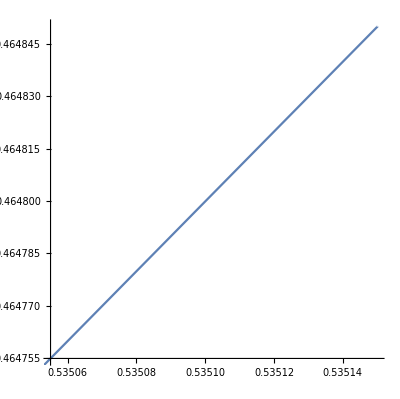

```mathematica
c=LightCurveoutOut[4]
```

```mathematica
PhotonTimeoutIn[r_,ro_]:=r-ro+Rs*Log[-(r-Rs)/(ro-Rs)];
```

```mathematica
LightCurveoutIn[ro_]:=ParametricPlot[{Yrightin[PhotonTimeoutIn[r,ro],r],Yupin[PhotonTimeoutIn[r,ro],r]},{r,0,9.999999}]
```

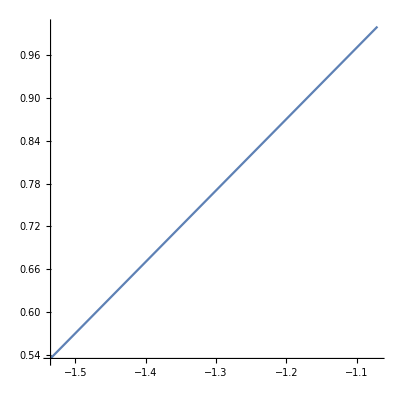

```mathematica
d=LightCurveoutIn[4]
```

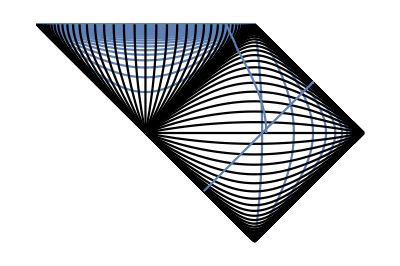

```mathematica
Show[complete,a,b,c]
```

```mathematica
LightCurveinOut[ro_]:=ParametricPlot[{Yrightout[-PhotonTimeoutOut[r,ro],r],Yupout[-PhotonTimeoutOut[r,ro],r]},{r,1.0000001,100}]
```

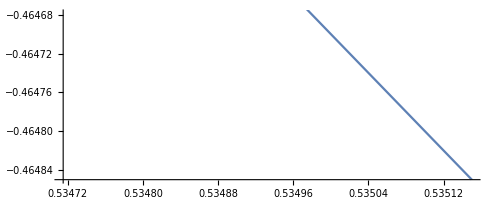

```mathematica
e=LightCurveinOut[4]
```

```mathematica
LightCurveinIn[ro_]:=ParametricPlot[{Yrightin[-PhotonTimeoutIn[r,ro],r],Yupin[-PhotonTimeoutIn[r,ro],r]},{r,0,9.999999}]
```

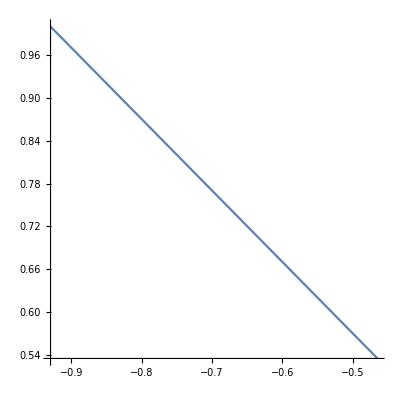

```mathematica
f=LightCurveinIn[4]
```

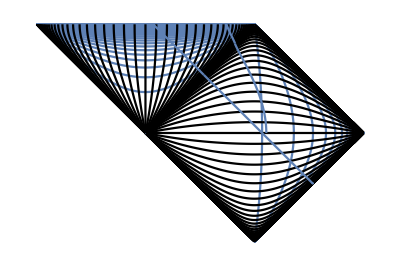

```mathematica
Show[complete,a,b,f,e]
```

```mathematica
Yright[ct_,r_]:=Which[r≥Rs,Yrightout[ct,r],0≤r,Yrightin[ct,r]];
Yup[ct_,r_]:=Which[r≥Rs,Yupout[ct,r],0≤r,Yupin[ct,r]]
```

```mathematica
PhotonTime[r_,ro_]:=r-ro+Rs*Log[(r-Rs)/(ro-Rs)];
```

```mathematica
LightCurve[ro_]:=ParametricPlot[{Yright[PhotonTime[r,ro],r],Yup[PhotonTime[r,ro],r]},{r,0,100}]
```

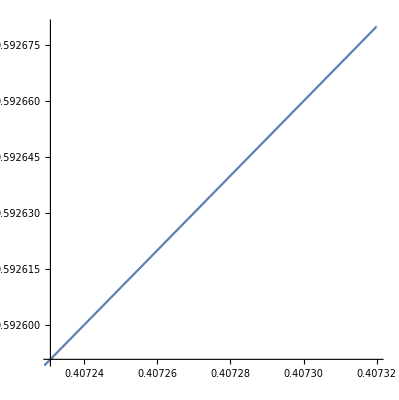

```mathematica
o=LightCurve[3.5]
```

```mathematica
InLightCurve[ro_]:=ParametricPlot[{Yright[-PhotonTime[r,ro],r],Yup[-PhotonTime[r,ro],r]},{r,1.0000001,100}]
```

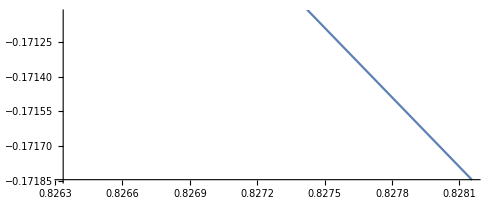

```mathematica
p=InLightCurve[7]
```

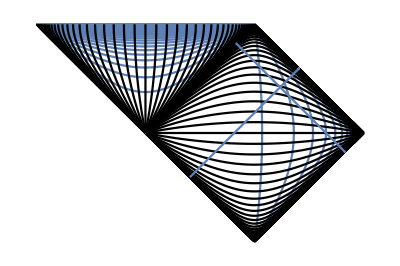

```mathematica
Show[complete,p,o]
```

```mathematica
ManCurve[ro_]:=ParametricPlot[{Yright[tFF[ro,η],rFF[ro,η]],Yup[tFF[ro,η],rFF[ro,η]]},{η,0,π}]
```

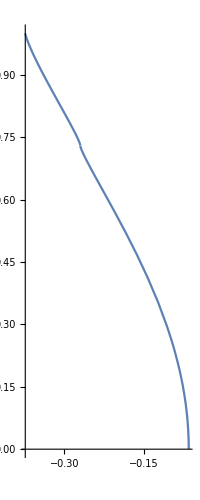

```mathematica
q=ManCurve[3.7]
```

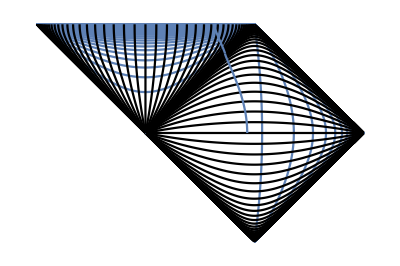

```mathematica
Show[complete,q]
```